```mathematica
(*由五连杆和电机定子的质量分布参数算出两腿质量分布参数的函数*)
LegCalcu[L0_,L_,l_,I_,m_]:=(
Module[{q0,q1,q2,q3,q4,Ic1,Ic2,Ic3,Ic4,Ic5,Icom,d1,d2,d3,d4,d5,r1,r2,r3,r4,r5,rcom,m0,Lw},
{q0,q1,q2,q3,q4}=VMCInverseSolution[L0,90,{L[[1]],L[[2]],L[[3]],L[[4]],L[[5]]}][[3]];
(*====================求解等效腿的质量分布====================*)
(*得各质心矢量*)
r1={l[[1]]Cos[q1],l[[1]]Sin[q1]};
r2={L[[1]]Cos[q1]+l[[2]]Cos[q2],L[[1]]Sin[q1]+l[[2]]Sin[q2]};
r3={L[[4]]Cos[q4]+l[[3]]Cos[q3]+L[[5]],L[[4]]Sin[q4]+l[[3]]Sin[q3]};
r4={l[[4]]Cos[q4]+L[[5]],l[[4]]Sin[q4]};
r5={L[[1]]Cos[q1]+L[[2]]Cos[q2],L[[1]]Sin[q1]+L[[2]]Sin[q2]};
m0=m[[1]]+m[[2]]+m[[3]]+m[[4]]+m[[5]];

rcom=Collect[Expand[m[[1]]r1+m[[2]]r2+m[[3]]r3+m[[4]]r4+m[[5]]r5],{Cos[q1],Sin[q1],Cos[q2],Sin[q2],Cos[q3],Sin[q3],Cos[q4],Sin[q4]}]/m0;
(*求解转动惯量*)
d1=Norm[r1-rcom];Ic1=I[[1]]+m[[1]]d1^2;
d2=Norm[r2-rcom];Ic2=I[[2]]+m[[2]]d2^2;
d3=Norm[r3-rcom];Ic3=I[[3]]+m[[3]]d3^2;
d4=Norm[r4-rcom];Ic4=I[[4]]+m[[4]]d4^2;
d5=Norm[r5-rcom];Ic5=I[[5]]+m[[5]]d5^2;
Icom=Ic1+Ic2+Ic3+Ic4+Ic5;
Lw=L0-Norm[rcom-{L[[5]]/2,0}];
Return[{Lw,Icom,m0}];
];
);
(*系统参数配置*)
g=9.81;
Subscript[m, b]=8.548;(*机体质量*)
Subscript[I, b]=0.2997272;(*机体转动惯量*)
Subscript[I, z]=0.2527;(*机体绕z轴转动惯量*)
Subscript[l, c]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[R, l]=0.251;(*两轮间距的一半*)
Subscript[m, w]=0.63;(*驱动轮质量*)
Subscript[I, w]=0.004301;(*驱动轮转动惯量*)
Subscript[R, w]=0.065;(*驱动轮半径*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;(*五连杆长度*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;(*五连杆质心位置*)
Subscript[I, 1]=0.003993;Subscript[I, 2]=0.064379;Subscript[I, 3]=0.060525;Subscript[I, 4]=0.003993;(*五连杆转动惯量*)
Subscript[m, 1]=0.211;Subscript[m, 2]=0.390;Subscript[m, 3]=0.204;Subscript[m, 4]=0.211;(*五连杆质量*)
Subscript[I, wm]=0.000813;(*电机定子转动惯量*)
Subscript[m, wm]=0.10;(*电机定子质量*)
```

0.144945+0.0567447 x-0.0982505 x^2

-0.0430315+0.65987 x

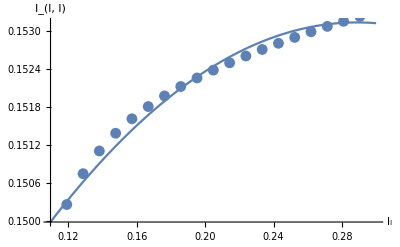

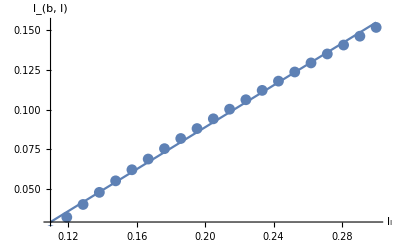

```mathematica
(*腿部质心与转动惯量拟合*)
Get["VMCsolution.m",Path->NotebookDirectory[]];
(*循环迭代*)
sampleNum=21;(*循环次数*)
YI=Array[0,{sampleNum}];
YL=Array[0,{sampleNum}];
Do[
(*输入量控制*)
Subscript[l, l]=0.10+0.2*(cnt1)/sampleNum;
(*由五连杆和电机定子的质量分布参数算出两腿质量分布参数*)
para=LegCalcu[Subscript[l, l],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,l]=para[[1]];Subscript[I, l,l]=para[[2]];Subscript[m, l]=para[[3]];Subscript[l, b,l]=Subscript[l, l]-Subscript[l, w,l];
(*数据记录*)
YI[[cnt1]]={Subscript[l, l],Subscript[I, l,l]};
YL[[cnt1]]={Subscript[l, l],Subscript[l, b,l]};
,{cnt1,sampleNum}];
KI= Fit[YI,{1,x,x^2},{x}]
KL= Fit[YL,{1,x},{x}]
Show[{Plot[KI, {x, YI[[1,1]], YI[[sampleNum,1]]},Axes->{True,True}, AxesLabel->{"l_l","I_(l, l)"}],ListLinePlot[YI,Joined->False]}]
Show[{ Plot[KL, {x, YL[[1,1]], YL[[sampleNum,1]]},Axes->{True,True}, AxesLabel->{"l_l","l_(b, l)"}],ListLinePlot[YL,Joined->False]}]
```

```mathematica
(*K矩阵无拟合*)
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{100,200,800,30,100,10,100,10,8000,500}];
Subscript[R, lqr]=DiagonalMatrix[{20,20,100,100}];
(*由五连杆和电机定子的质量分布参数算出两腿质量分布参数*)
Subscript[l, l]=0.15;(*设置左腿长*)
Subscript[l, r]=0.15;(*设置右腿长*)
Get["VMCsolution.m",Path->NotebookDirectory[]];
para=LegCalcu[Subscript[l, l],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,l]=para[[1]];Subscript[I, l,l]=para[[2]];Subscript[m, l]=para[[3]];Subscript[l, b,l]=Subscript[l, l]-Subscript[l, w,l];
para=LegCalcu[Subscript[l, r],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,r]=para[[1]];Subscript[I, l,r]=para[[2]];Subscript[l, b,r]=Subscript[l, r]-Subscript[l, w,r];
(*LQR计算*)
Subscript[A, op]=Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op]=Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[A, op]=SparseArray[Subscript[A, op]];
Subscript[B, op]=SparseArray[Subscript[B, op]];
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr]
```

{{-1.55655,-3.14219,-1.99572,-0.138159,-13.4528,-2.31259,1.30728,-0.0103002,-3.18659,-1.21733},{-1.55655,-3.14219,1.99572,0.138159,1.30728,-0.0103002,-13.4528,-2.31259,-3.18659,-1.21733},{0.124211,0.237821,-1.78981,-0.700304,5.75135,0.867569,-4.84826,-0.705913,-6.6076,-2.05861},{0.124211,0.237821,1.78981,0.700304,-4.84826,-0.705913,5.75135,0.867569,-6.6076,-2.05861}}